# Monte Carlo direct method

Monte Carlo integration uses random sampling of a function to numerically compute an estimate of its integral. 
Suppose that we want to integrate the one-dimensional function f (x) from a to b:

F=∫_a^b f(x)ⅆx

The integral sign ∫ represents integration. 
The symbol dx, called the differential of the variable x, indicates that the variable of integration is x. 
The function f(x) to be integrated is called the integrand. A function is said to be integrable if the integral of the function over its domain is finite.
The points a and b are called the limits of the integral. An integral where the limits are specified is called a definite integral. 
The integral is said to be over the interval [a, b].


Now let's first approach it with classical integration.

Our integrand is the function : 7x-8.5 x^2+3 x^3 and its domain ϵ R[0,2].

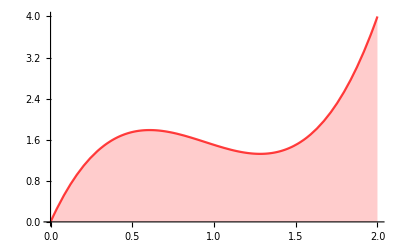

```mathematica
Clear[f,x];
f[x_]=7x-8.5 x^2+3 x^3;
Plot[f[x],{x,0,2},Filling->Axis,PlotStyle->{Red, Opacity[0.75]},PlotRange->Full]
```

Integration is generally referred as to find the area under the fnc curve.

Now the general approach for numerical deterministic integration is to :
- subdivide the area under the curve by many rectangular bins, 
- calculate for each their respective area and 
- eventually sum then all up

```mathematica
Clear[a,b,di,intervals];
a=0; b=2; (* domain *)
nbins=25; (* integration steps *)
di=(b-a)/nbins; (* base *)
intervals=Range[a,b,di]; (* intervals *)
```

Above result is actually the base length of our rectangular bins. In fact, we subdivided the x-axis extension of our integrand by n-steps.
Now we need to multiply the base by the height to find the area our rectangles. 
What is the height of our rectangles ? It’s the integrand evaluation at that point.

One little caveat is that we can start from the left of our basis or from the right or from the center.

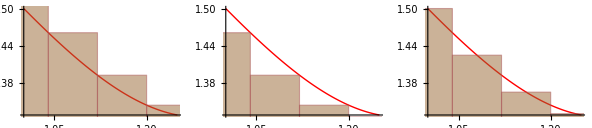

```mathematica
Framed@GraphicsRow[Plot[f[x],{x,1,1.25},PlotStyle->{Red,Thick},Epilog->{Opacity[.5],Brown,EdgeForm[Darker@Pink],Rectangle@@@(Transpose/@Transpose[{Partition[intervals,2,1],Partition[Riffle[f/@#@intervals,0,{1,-2,2}],2]}])},ImageSize->Small]&/@{Most,Rest,MovingAverage[#,2]&}]
```

```mathematica
leftSum=Sum[di*f[i],{i,Most@intervals}];
rightSum=Sum[f[i] di,{i,Rest@intervals}];
middleSum=Sum[f[i+di/2] di,{i,Most@intervals}];
N@{leftSum,rightSum,middleSum}
```

{3.1744,3.4944,3.3328}

Above is the result of nbins integration =25 (i.e. we subdivided the x by 25).
Let’s use Mathematica symbols to calculate the correct true answer and compare it with our.
We see the middle point sum method is more precise  than the other twos.

```mathematica
NIntegrate[f[x],{x,0,2}]
```

3.33333

We can still use Mathematica and NIntegrate to do what we’ve done manually above.

```mathematica
NIntegrate[f@x,{x,0,2},
Method->{"RiemannRule","Type"->#,"Points"->25}]&/@{"Left","Right"}
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.87492}. NIntegrate obtained 3.33325 and 0.000159611 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.875}. NIntegrate obtained 3.33342 and 0.000159356 for the integral and error estimates.

{3.33325,3.33342}

If we keep increasing the integration steps we’ll keep getting closer and closer to the correct answer. 
To what point we should keep increasing our number of steps ? To have them an infinitesimal width ⅆx.

When the step width approaches ⅆx we don’t talk anymore about summation but about integration and use the integral symbol.

```mathematica
∫_0^2 (7x-8.5 x^2+3 x^3)ⅆx
```

3.33333

========================================================================================

Now let’s approach this with Monte Carlo.

We can approximate this integral by averaging samples of the function f at uniform random points within the interval. 
Given a set of N uniform random variables X_i ∈ [a,b) with a corresponding PDF of 1/(b − a) (i.e. the pdf of a uniform distribution)
the Monte Carlo estimator for computing F is

⟨F^N⟩=(b-a)1/(N-1)∑_(i=0)^N f(X_i)

(take care that the above is actually the sample mean of X_i, aka the mean estimate, also called the primary MC estimator)
The random variable X_i ∈ [a,b) can be constructed by :
- warping a canonical random number uniformly distributed between zero and one, ξ_i ∈ [0, 1):

X_i=a+ξ_i(b-a)

With that, our estimator becomes :

⟨F^N⟩=(b-a)1/N∑_(i=0)^(N-1) f(a+ξ_i(b-a))

Note that ⟨F^N ⟩ means ‘approximating f with N samples’ and since ⟨F^N⟩ is a function of X_i, it’s itself a random variable.

```mathematica
n=600;
(b-a)1/n∑_(i=0)^n f[a+RandomReal[]*(b-a)]//N
Sum[f[a+RandomReal[]*(b-a)],{i,0,n}]*(2/(n-1))

(* while the above procedures are the same they will return different results due to the random numbers *)
```

3.35581

3.41758

```mathematica
f[a+RandomReal[]*(b-a)]
```

1.48064

======================================================================================================
[LT->Theory->2014 - Monte Carlo Integration Tecniques]

It is easy to show that the expected value ⟨F^N⟩ is in fact F.

First recall the proofs about Expected Values and Variance.
The expected value of a random variable Y=f(X) over a domain μ(x) is

E[Y]=∫_(μ(x)) f(x)pdf(x)ⅆx

while its variance is

σ^2[Y]=E[(Y-E[Y])^2] = E[(Y-μ_y)^2]

where σ, the standard deviation, is the square root of the variance

E[aY]=aE[Y]
σ^2[aY]=a^2 σ^2[Y]

furthermore, the expected value of a sum of random variables Y_i is the sum of their expected values

E[∑_i Y_i]=∑_i E[Y_i]      (* this is called, the linearity of the expectation value *)

From there we derive a simpler expression for the variance

σ^2[Y]=E[Y^2]-E[Y]^2 (* see expectation algebra in part1 *)

σ^2[∑_i Y_i]=∑_i σ^2[Y_i] (* for uncorrelated randoms *)

With the above in mind we can demostrate that ⟨F^N⟩ is in fact F
(so that the error here would be zero.. ie ⟨F^N⟩ is an unbiased estimator)

E[⟨F^N⟩]=E[(b-a)1/N∑_(i=0)^(N-1) f(X_i)]
=(b-a)1/N∑_(i=0)^(N-1) E[f(X_i)] (*from 4 and 3a*)
=(b-a)1/N∑_(i=0)^(N-1) ∫_a^b f(x)pdf(x)ⅆx  (*from 1*)
=1/N∑_(i=0)^(N-1) ∫_a^b f(x)ⅆx  (*since pdf(x)=1/(b-a)*)
=∫_a^b f(x)ⅆx 
=F|⟨⟨F⟩⟩

Eventually due to ‘the law of large numbers’ the estimator ⟨F^N⟩ becomes closer and closer to F

Pr{lim_(N→∞) ⟨F^N⟩=F}=1
Pr{lim_(N→∞) ⟨A^-⟩=⟨A⟩}=1

So with Mathematica code we can approach this with :

```mathematica
m=100;
1/m∑_(i=0)^m ((b-a)1/n∑_(i=0)^n f[a+RandomReal[]*(b-a)])//N
```

3.37763

========================================================================================
[LT->Theory->Sampling->MCErrorAnalysis->Estimating Errors Reliably in Monte Carlo Simulations]
( This also anticipates the MC error derivation we’ll find below )

However take care that in some literature something is the estimate  F^- and something else is ⟨F⟩ which is the true expectation, 
there, the above relation is defined as ⟨A^-⟩=⟨A⟩ , so that the deviation of ⟨A^-⟩ from the true expectation ⟨A⟩ is a fluctuating quantity ∆_A .

So below, 
A^- is the mean estimate of A while 
⟨A⟩ is the true expected value of A (sometimes written like ⟨⟨A⟩⟩ ). And 
⟨A^-⟩ is the expected mean estimate of A.

More generally it would be written as Â=A (where the hat^ stays for expectation as ⟨ ⟩. However then we don’t have the upper space for another symbol so to write the expected mean value of A with the ^ notation, we use the μ that stays for mean.. μ̂ is the expected mean value of A, ie. ⟨A^-⟩

And just to make things easier ;) we may add the distinction between an estimate and an estimator.
If we write μ̂=x^- ; we want to say that the estimate μ is the mean x^-. Formally this is written as θ̂=x^-
But if we wanna talk about the estimator (not the estimate) then we should use the uppercase theta Θ .


Anyway :) due to the linearity of the expectations

⟨A^-⟩=⟨1/N∑_(i=1)^N A_i⟩=1/N∑_(i=1)^N ⟨A_i⟩=1/N∑_(i=1)^N ⟨A⟩=⟨A⟩

where ⟨A⟩

⟨A⟩=∑_x A(x)p(x)

and

A_i≡A(x_i)

Similar reasoning allows the calculation of the average of the square of the sample mean

⟨(A^-)^2⟩=⟨(1/N∑_(i=1)^N A_i)^2⟩=1/N∑_(i=1)^N ∑_(j=1)^N ⟨A_i A_j⟩
=1/N^2∑_(i=1)^N ⟨A_i^2⟩+(N-1)/N⟨A⟩^2

=1/N⟨A^2⟩+(N-1)/N⟨A⟩^2

where we have inserted the definition of the average,

A^-=1/N∑_(i=1)^N A_i

then used the linearity of the expectation value, 
and also exploited the fact that for independent samples x_i and x_j, the expectation value for i≠j factorizes as

⟨A_i A_j⟩=⟨A_i⟩⟨A_j⟩=⟨A⟩^2

The statistical error ∆_A, the root-mean-square deviation of the sample mean A^- from the true expectation value ⟨A⟩, 
is thus given by

∆_A^2≡⟨(A^--⟨A⟩)^2⟩=1/N^2∑_(i=1)^N ⟨A_i^2⟩-1/N⟨A⟩^2
= 1/N(⟨A^2⟩-⟨A⟩^2)≡1/N σ_A^2

which is the basis of the central limit theorem.

It is, however, more useful to express the error in terms of the sampled A_i ’s.
A naïve guess would be to estimate the variance as (A^2)^--(A^-)^2, where
(one is the average of the squared A and the other is square of the averaged A)

(A^2)^-≡1/N∑_(i=1)^N A_i^2

If we calculate the expectation values via (6) we get

⟨(A^2)^--(A^-)^2⟩=(N-1)/N σ_A^2

Thus the estimator is

σ_A^2|Var[A]≈N/(N-1)((A^2)^--(A^-)^2)

where the (small) fluctations in the right-hand side have been ignored. 
Eventually, taking the square root , we obtain the final result

∆_A=√(Var[A]/N)≈√(((A^2)^--(A^-)^2)/(N-1))

The -1 in the denominator, which is irrelevant for large values of N, reflects the loss of one piece of information in calculating the sample mean.

========================================================================================

Btw, with standard integration we are almost there with just 25 ‘samples’ ... 
how it comes that with Monte Carlo we need 50000 samples to get there ?
(Or how can a random array be better than a grid ?)

Now the error for the midpoint method (Riemann sum) is

∝ (b-a)/N^d

this is because for a monotone function in a-b
-Graphics-

and more generally :

Er∝M(b-a)^2/n^d

========================================================================================
[LT->Theory->Sampling->MCErrorAnalysis->Error Estimates for the Monte Carlo Method]

while for the error with Monte Carlo method 

we first draw some introduction. We know the following relationship between our estimation and true value

θ̂=θ +error

We saw just above the potentially for an unbiased estimator the error will be 0 because

θ̂-θ = 0

That is, θ̂ is unbiased if its probability sampling distribution is ‘centered’ at the true value of the parameter (outcome).

-Graphics-

We have the following entities for our setup :

x^-   is the simulated (or the estimated) output  (ie. the above A^- ,  F^N or the below (μ̂)_n)
μ_x is the true expected output, (ie. the above ⟨A⟩ or the below μ)
x_i  is the generated sample where i=1 to N, (ie. replicates (A_i) of the outcome of a certain f[x] )
(x⃗)_i  is the configurator (also called the locator)

Practically it is like this :

x^-   = (b-a)1/n∑_(i=0)^n f[a+RandomReal[]*(b-a)]
μ_x =  ∫_0^2 (7x-8.5 x^2+3 x^3)ⅆx
x_i  =  f[a+RandomReal[]*(b-a)]
(x⃗)_i  =  RandomReal[]

And it works like this.. 
every time we run the Mathematica code for x^- we’ll get different results (just go above and run and re-run the code :).
Now the fluctuating quantity from the result will deviate a certain ∆_x from the true expected result and that is the Monte Carlo Error.
With other words, according to the Central Limit Theorem, x^- is normally distributed around μ_x with a standard deviation ∆_x .
Or also that, the rate of convergence of our simulation for N is ∆_x .


This can be seen also as

(x^-)_1=f(x⃗)

when x⃗ is distributed uniformly, the estimator (called primary estimator) is unbiased so that its expected value is the integral.

E[(x^-)_1]=I

Now the function f(x⃗) is itself a random variable with an arbitrary distribution and typically a large variance.
A more practical MC estimator is obtained by averaging a fixed number of (say N) primary estimates

(μ^-)_N=∑f((X^-)_i)/N

Such secondary estimators are known to be unbiased and approach a Gaussian distribution as N→∞ and if the primary estimator has finite var.

So, when we refer to the estimation of a primary estimator we use lowercase x^-
when we refer to the estimation of a secondary estimator we use uppercase X^-, so the single outcome X_i=x^-

X^-|(μ^-)_N=1/N∑_(i=1)^N (x^-|X_i)=1/N∑_(i=1)^N (1/n∑_(i=1)^n x_i)

Now, let’s see the derivation for the above.
Below we are subtracting the true expected value from the mean of the simulation to see how accurate is x^- as an estimate of μ_x

E[X^--μ_x]=E[X^-]-μ_x=E[1/N∑_(i=1)^N X_i]-μ_x=1/N∑_(i=1)^N E[X_i]-μ_x

Since x_i occurs from random sampling, then the expectation of x_i (x^-)  equals the true expected value μ_x , thus we have

E[X^--μ_x]=1/N Nμ_x-μ_x=0

This result shows that on average, the error in using x^- to approximate μ_x is zero.
(when an estimator gives an expected error of zero, it is called an unbiased estimator)

Next, to quantify the variability in X^-, we use the variance of (X^--μ_x), 
noting that the (variance of μ_x) is zero as it is a constant (because comes from the true expected value ?)

Var[X^--μ_x]=Var[x^-]-Var[μ_x]=Var[X^-]
=Var[(∑_(i=1)^N X_i)/N]=1/N^2 Var[∑_(i=1)^N X_i]

Because the Monte Carlo method draws independent, random samples, 
the variance of the sum of the samples x_i, is the sum of their variances (see Variance algebra on part1). 
Therefore

Var[X^--μ_x]=1/N^2[∑_(i=1)^N Var[X_i]]=1/N^2 Nσ_x^2=σ_x^2/N
μ_x≡E[X^-]=μ_x, σ_x^2≡E[(X^--μ_x)^2]=σ_x^2/N=σ_x 1/(√N)

========================================================================================
[LT->Theory->Sampling->MCErrorAnalysis->Basics of Direct Monte Carlo]

In a more straightforward way.
Since all the random variables X_i (ie. the generated samples) in our sample have mean µ, the mean of the sample mean is

E[(μ̂)_n]=μ

In words, we can say that given a particular design (ie. f_x() ), let 
μ denote some target quantity of interest (the true expected value) and 
(μ̂)_n denote the Monte Carlo expected estimate of μ from a simulation with N replicates (where each generated replicate is X_n)
(so it could be written just as ⟨μ⟩=μ that belongs to the notation above as  ⟨A^-⟩=⟨A⟩ or ⟨F^N⟩=F)

In the language of statistics, (µ̂)_n is said to be an unbiased (mean) estimator of µ.

We assume that the X_i have finite variance. 
Since they are identically distributed, they have the same variance σ.
Since they are also independent, we have (from variance algebra, that the variance of the sum of the samples x_i, is the sum of their variances)

Var[∑_(i=1)^N X_i]=Nσ^2

(aka the variance of the sum of all the outcomes of X_i is proportional to the variance of the sample times Nsamples (ie. sum of equal variances))
and so the variance of the sample mean is

Var[(μ̂)_n]=1/N^2 Var[∑_(i=1)^N X_i]=σ^2/N

Thus the difference of μ_N from μ should be of order σ/√N
This is written also as

σ[⟨F^N⟩]∝1/(√N)

========================================================================================
In other words, we're sayin that for infinite (N) samples the mean of the simulation is equal to true expected value of the simulation, 
where for Nsamples instead it is just proportional to and the difference is the MC error .. that is the same as saying that 
the rate of convergence of our Monte Carlo simulation to the exact value is, 1/√N.

Here we see that for standard deterministic quadratures the error is 1/N^d while for Monte Carlo direct method the error is 1/√N.
This means that the standard approach has a faster rate of convergence than Monte Carlo. 
For example it approaches 0.04 error with just 25 samples where for Monte Carlo we need around 600.

```mathematica
N[1/25]
N[(1/√600),1]
```

0.04

0.04

Another thing we see is that, - to halve the error in a Monte Carlo simulation we need x4 samples (that is the square of the improvement)
(or in other words, that the standard error decreases with the square root of the sample size)

```mathematica
{N[(1/√(600*4)),1],"halved the above error"}

(* if we want 10 time less the actual error(0.04) ?.. we need a *10^2 Nsamples boost *)
N[(1/√(600*10^2)),1]
```

{0.02,halved the above error}

0.004

However Monte Carlo error does not belong to the dimensions involved while the standard error does, effectively standard integration techniques suffer from the curse of dimensionality, where the convergence rate becomes exponentially worse with increased dimensions. It can be seen that only for integrals with more than 6 dims the MC error starts to be better than the standard. The smoothness of the integral can also play a part .. where it’s narrow, standard quadratures have more problem sampling it than Monte Carlo.

Take care that being the usual approach to estimate σ as well as μ and then take your error magnitude to be σ/√n , the MC error is just a probabilistic error bound (there is no guarantee that the expected accuracy is achieved in any particular case). Same goes for  “convergence” that means that you will never get an exact answer from Monte-Carlo but increasingly good approximations.


========================================================================================
[LT->Theory->Sampling->MCErrorAnalysis->Basics of Direct Monte Carlo]

The central limit theorem gives a more precise statement of how close (μ̂)_n is to µ. It says :
- Let X_n be an iid sequence such that E[|X, n|^2]<∞.
- Let μ=E[X_n] and
- Let σ^2 be the variance of X_n ie. σ^2=E[X_n^2]-E[X_n]^2
then

1/(σ √n)∑_(k=1)^n (X_k-μ)

converges in distribution to a standard normal random variable.
This means that

lim_(n→∞) P(a≤1/(σ √n)∑_(k=1)^n (X_k-μ)≤b)=∫_a^b 1/(√(2π))ⅇ^(-x^2/2)ⅆx

In terms of the sample mean, the central limit theorem says that ((μ̂)_n-μ)√n σ converges in distrbution to a standard normal distribution.

However the statement of the central limit theorem involves σ^2. It is unlikely that we know σ^2 if we don’t even know µ. 
So we must also use our sample to estimate σ^2. 

The usual estimator of the variance σ^2 is the sample variance. 
It is typically denoted by s^2, but we will denote it by s_n^2 to emphasize that it depends on the sample size. It is defined to be

s_n^2=1/(n-1)∑_(i=1)^n (X_i-(μ̂)_n)^2

An application of the strong law of large numbers shows that s_n^2→σ^2. Since ((μ̂)_n-μ)√n/σ converges in distribution to a standard normal distribution and that s_n^2→σ^2 converges almost surely (a.s.) to σ^2, a standard theorem in probability implies that ((μ̂)_n-μ)√n/s_n converges in distribution to a standard normal. (In statistics the theorem being used here is usually called Slutsky’s theorem.) 

So we have the following variation on the central limit theorem :
- Let X_n be an iid sequence such that E[|X, n|^2]<∞.
- Let μ=E[X_n] and
- Let σ^2 be the variance of X_n ie. σ^2=E[X_n^2]-E[X_n]^2
then

((μ_n-μ)√n)/s_n

converges in distribution to a standard normal random variable.
This means that

lim_(n→∞) P(a≤((μ_n-μ)√n)/s_n≤b)=∫_a^b 1/(√(2π))ⅇ^(-x^2/2)ⅆx

The central limit theorem can be used to construct confidence intervals for our estimate (μ̂)_n for μ.

We want to construct an interval of the form [(μ̂)_n-ϵ, (μ̂)_n+ϵ] such that 
the probability μ in this interval is (1-α) where the confidence level (1-α) is some number close to 1, ie. 95%.

So let Z be a random variable with the standard normal distribution. 
Then note that μ belongs to [(μ̂)_n-ϵ,(μ̂)_n+ϵ] if and only if (μ̂)_n belongs to [μ-ϵ,μ+ϵ].

The central limit theoreom says that

P(μ-ϵ≤(μ̂)_n≤μ+ϵ)=P(-ϵ≤(μ̂)_n-μ≤ϵ)
=P(-(ϵ √n)/s_n≤(((μ̂)_n-μ)√n)/s_n≤(ϵ √n)/s_n)≈P(-(ϵ √n)/s_n≤Z≤(ϵ √n)/s_n)

Let z_c be the number such that P(-z_c≤Z≤z_c)=1-α.
Then we have (ϵ √n)/s_n= z_c ie. ϵ=z_c s_n/√n. 
Thus our confidence interval for μ is

(μ̂)_n±(z_c S_n)/(√n)

(btw, Z_c stays for Z critical value).

Common choices for (1−α) are 95% and 99%, for which z_c ≈ 1.96 and z_c ≈ 2.58, respectively.
(The central limit theorem is only a limit statement about what happens as the sample size n goes to infinity. 
How fast the distribution in question converges to a normal distribution depends on the distribution of the original random variable X).

It’s easy to see that if we are looking for an error around 1std, being the estimated distribution a standard normal distribution (see part1 for  the 68-95-99.7 rule) we’ll fall into just 68% of the distribution or in other words that we have around 68% probability to be there within 1std error.

On the other side as seen above, if we really want a strict confidence interval, ie. we wanna be almost (ie. 99.7%) sure that our estimate is almost the true expectation than we’ll have to take a fairly big potential error, ie. around 3std. 


Eventually keep in mind that from a practical point of view, what is important is not how many samples are needed to achieve a given level of accuracy, but rather how much CPU time is need to achieve that accuracy. Suppose we have two Monte Carlo methods that compute the same thing. They have variances σ_1^2 and σ_2^2. Let τ_1 and τ_2 be the CPU time needed by the methods to produce a single sample. With a fixed amount Τ of CPU time we can produce Subscript[N, i]=Τ/τ_i samples for the two methods. So the errors of our two methods will be

σ_i/(√N_i)=(σ_i √τ_i)/(√Τ)

Thus the method with the smaller σ_i^2 τ_i is the better method.

On a final note, take care that when

lim_(n→∞) F_n→𝒩(0,1)

we’re saying that the limiting distribution for a large set of sample means is the Standard Normal Distribution.
In other words, a sample mean can have any arbitrary distribution.. when we go for repeated simulation that arbitrary distribution tends to a standard normal distribution, because of that is called limiting distribution or also asymptotic distribution.

========================================================================================
Another way to put it is that, we know from part1 (Central Limit Theorem) that to ‘standardize’ a normal distribution we have

z=(X^--μ)/(σ √n)

Then for example, because the area under the standard normal curve between and 1.96 is 0.95, we can write

P(-1.96<(X^--μ)/(σ √n)<1.96)=0.95

Let’s now manipulate the inequalities inside the parentheses so that they appear in the (confidence) interval form.
Basically we’re rewriting the eq in terms of μ.
Multiply both sides by σ/√n

-1.96 σ/(√n)<X^--μ<1.96 σ/(√n)

Subtract X^- from each term

-X^--1.96 σ/(√n)<-μ<-X^-+1.96 σ/(√n)

Eventually multiply through by -1 to make μ without the minus in front (that will reverse the direction of each inequality)

X^-+1.96 σ/(√n)>μ>X^--1.96 σ/(√n)

that is

X^--1.96 σ/(√n)<μ<X^-+1.96 σ/(√n)

with the interval

{X^--1.96 σ/(√n),X^-+1.96 σ/(√n)}

This can be paraphrased as “there’s a probability of .95 that the random interval includes or covers the true value of μ”.

-Graphics-

However take care that the confidence level is not so much a statement about any particular interval. Instead it pertains to what would happen if a very large number of intervals were to be constructed using the same CI formula... aka it applies to a long sequence of replications of an experiment rather than just a single replication.

Example (Confidence Intervals)

You want to rent an unfurnished one-bedroom apartment in Durham, NC next year. 
The mean monthly rent for a random sample of 60 apartments advertised on Craig’s List is $1000.
Assume a population standard deviation of $200. Construct a 95% confidence interval.

```mathematica
Clear[x,σ,n,α,Z];
x=1000;
σ=200;
n=60;
α=95/100;
Z=Abs[InverseCDF[NormalDistribution[0,1],(1-α)/2]];

{"Confidence Interval->",x-Z σ/(√n), x+Z σ/(√n)}//N
```

{Confidence Interval->,949.394,1050.61}

========================================================================================
Now, let’s recap what we saw till here we some examples.


Let’s say we have this function to integrate over (0,π)

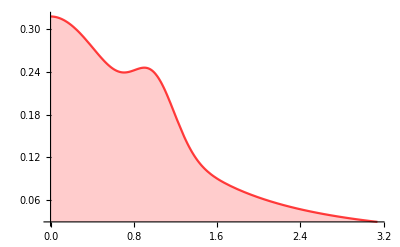

{True value,0.441907}

```mathematica
Clear[f,x,a,b, w, n, tValue, eValue];
f[x_]=2/(2 (1+x^2) π)+(2 ⅇ^(-25/2 (-1+x)^2))/(10 √(2 π));
a=0;
b=π;
w=b-a;
Plot[f[x],{x,a,b},Filling->Axis,PlotStyle->{Red, Opacity[0.75]},PlotRange->Full]
tValue = ∫_a^b f[x]ⅆx//N;
{"True value",tValue}
```

Let’s calculate our estimated result with Monte Carlo.

```mathematica
n=10^4;
SeedRandom[12345];

(* 3 equivalent ways with Mathematica *)
w 1/n∑_(i=0)^n f[a+RandomReal[]*w]//N

Sum[f[a+RandomReal[]*w],{i,0,n}]*(w/n)

ests= Table[f[a+RandomReal[]*w],{i,n}]*w; (* with this one we keep the estimates so we can deal with error analysis *)
Mean[ests]
```

0.437377

0.446679

0.440544

Now, let’s deal with errors aka Monte Carlo Analysis that will return a serie of Monte Carlo statistics (MCS) of interest. 

Constructing MCSs is simply a matter of organizing a “generate–analyze–summarize” scheme so that particular datasets and analysis procedures can be emulated and studied over a wide number of random replications.


Let’s start by using Mathematica buildin StandardDeviation and Variance symbols for our list of estimates

```mathematica
Variance[ests]
StandardDeviation[ests]
```

0.0987918

0.314312

We know that  an estimate of the variance from Monte Carlo samples is given by the average of each sample’s error squared:
(where x^-=μ=μ_X=true mean result and (X̂)_n=estimated mean)

σ^2≈(∑_(n=1)^N ((x̂)_n-x^-)^2)/N

This is the Mean Squared Error (MSE) and the Monte Carlo Standard Error based on that is

MCSE=√((∑_(i=1)^N (((x̂)_n-x^-)^2-MSE)^2)/(N(N-1)))

```mathematica
Clear[sqr,MSE];
sqr=Sum[(ests[[i]]-tValue)^2,{i,n}];        (* numerator above *)
MSE=√(sqr/n)

MCSE = √(Sum[((ests[[i]]-tValue)^2-MSE)^2,{i,n}]/(n*(n-1)))
```

0.314299

0.00227576

If we don’t have the true outcome (most likely) we can use a fixed estimate as mean. 
Because we lose a degree of freedom in using the estimate as opposed to use the true value, we use N=N-1

σ^2≈(∑_(n=1)^N ((x̂)_n-x̂))/(N-1)

This is called ‘empirical standard error’ (Empirical SE)

σ≈√((∑_(n=1)^N ((x̂)_n-x̂))/(N-1))

And the Monte Carlo standard error based on that is

MCSE=EmpiricalSE/(√(2(N-1)))

```mathematica
Table[f[a+RandomReal[]*w],{i,n}]*w;
eValue=Mean[%];
√(Sum[(ests[[i]]-eValue)^2,{i,n}] *(1/(n-1)))

MCSE = %/√(2(n-1))
```

0.314313

0.00222264

BTW, if we wanna compare two error returns (from the same error model), we can use this formula

100((MCSE_1/MCSE_2)^2-1)

```mathematica
Quantity[100*((0.0021999/0.0021947)^2-1),"Percent"]
```

0.47443 %

Technically we got an increase in relative precision by a 0.47% ! ;)


Anyway, we see our estimated standarddeviations is coherent with the previous true standarddeviation.

Now let’s say it’s not practical for us to deal with the expected mean before running our simulation, as seen above (7) we can use the following to compute our standarddeviation. This works also ‘inline’ ie. for ‘running summations’ without having to keep the estimates in memory.
[LT->Theory->Sampling->MCErrorAnalysis->MonteCarloAnalysis]

√(((X^2)^--(X^-)^2)/(N-1))=N/(N-1)((∑_(n=1)^N (X̂)_n^2)/N-((∑_(n=1)^N (X̂)_n)/N)^2)

```mathematica
Clear[k,y];
k=Sum[(ests[[i]])^2,{i,n}] *(1/n);
y=(Sum[(ests[[i]]),{i,n}] *(1/n))^2;
σ̂=√(n/(n-1)*(k-y)) (* note that because it's an estimated error we use the ^hat over the σsigma *)
```

0.314312

========================================================================================
Till now we saw error analysis for a single simulation. 

Let’s see how to deal with multiple replications of a Monte Carlo simulation.

{true result,3.33333}

3.3349

3.32614

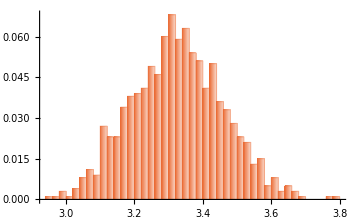

```mathematica
Clear[n,m,a,b,w, data00, data01, data02,f,x,tValue];
n=100;                                       (* n samples *)
m=1000;                                     (* n simulations *)
f[x_]=7x-8.5 x^2+3 x^3;    (* integrand *)
a=0; b=2;                               (* domain *)
w = b-a;                                   (* 'quadrature' width *)

{"true result", tValue=∫_a^b f[x]ⅆx }

(* (b-a)1/(n*m)∑_(i=0)^(n*m) f[a+RandomReal[]*(b-a)]; *)
data00=ParallelTable[f[a+RandomReal[]*w],{i,n*m}]*w;
Rnm=Mean[data00]


(* 1/m∑_(i=0)^m (w 1/n∑_(i=0)^n f[a+RandomReal[]*w]); *)
data01:=Table[f[a+RandomReal[]*w],{i,n}]*w;  (* same as the symbolic above but we keep the estimates *)
data02=ParallelTable[data01,m];                                   (* eval m times data01 (that itself evals fx *n times) *)
data03={};                                                                                    (* all replication means will be here *)
For[i=1,i<m+1,i++,                                                           (* dunno why but if we do Mean[data02] that should return m means.. *)
data=data02[[i]];                                                                  (* instead it return n means !? effectively we have m items ! *)
mm=Sum[data[[j]],{j,n}]*(1/n);                                (* let's do it manually ..................................... *)
AppendTo[data03,mm]
]
RnXm=Mean[data03]                                                                      (* mean of the replication means, ie. final average *)

Histogram[data03, 32,"Probability",PlotTheme->"WarmColor",ImageSize->Medium,ChartElementFunction->"FadingRectangle"]

(* the latter, approaches a standard normal distribution (thanks to CLT) as we can see when m is big enough but .. *)
(* if m is not big enough we can still get confidence intervals from a student-t distib where the degrees of freedom is (m-1) *)
Show[
Plot[PDF[NormalDistribution[0,1],x],{x,-9,9},PlotRange->Full ],
Plot[PDF[StudentTDistribution[16],x],{x,-9,9},PlotStyle->{Red, Opacity[0.75]} ]];
(* with enough degrees of freedom a student-t distribution approaches a gaussian distribution *)
(* left at 16 or at 20 the two plots almost coincide.. that's it ! With at least 20 repeats we have student-t -> stdgauss *)
```

So what are we doing here ? We’re not here to spank frogs, right ? :))

We first run a single simulation (with n*m samples=10^7).
Then we run multiple simulations (each with n samples=10^4) * (m=10^3) replicates.

At least in Mathematica, - the latter approach is always faster than the former (use AbsoluteTiming to check this)

Let’s first quantify the relative % of our simulations.

```mathematica
Interpreter["Percent"][100*((Rnm/RnXm)-1)]
```

0.263217 %

Let’s start our analysis with data00, ie. the one from the n*m simulation,
using Mathematica buildin stuff for that

```mathematica
Variance[data00]
StandardDeviation[data00]
```

1.77397

1.3319

Now go for the usual approach where we pretend to have the true value to compare against

```mathematica
Clear[sqr];

sqr=Sum[(data00[[i]]-tValue)^2,{i,n*m}];
{"variance",VARt=sqr/(n*m)}
{"std",STDt=√VARt}

{"MCSEt",√(Sum[((data00[[i]]-tValue)^2-STDt)^2,{i,n*m}]/((n*m)*((n*m)-1)))}
```

{variance,1.77395}

{std,1.3319}

{MCSEt,0.0119233}

Let’s take a full sim estimated outcome and use it as true value for our error estimation (aka empirical error)

```mathematica
Clear[eValue];
eValue=data03[[RandomInteger[100]]]; (* point estimator *)
{"variance",VARe=Sum[(data00[[i]]-eValue)^2,{i,n*m}] *(1/(n*m-1))}
{"std",STDe=√VARe}

{"MCSEe",MCSE = STDe/√(2((n*m)-1))}
```

{variance,1.82514}

{std,1.35098}

{MCSEe,0.00302089}

```mathematica
{"Theoretical VS Estimated STDerror",Interpreter["Percent"][100*((STDt/STDe)-1)]}
```

{Theoretical VS Estimated STDerror,-1.41215 %}

Here instead let’s pretend we don’t have a clue of what’s the true outcome will be, so we estimate the variance and std

```mathematica
Clear[k,y];
k=Sum[(data00[[i]])^2,{i,n}] *(1/n);
y=(Sum[(data00[[i]]),{i,n}] *(1/n))^2;
{"variance",VARes=n/(n-1)*(k-y)}
{"std",STDes=√VARes}
```

{variance,2.37231}

{std,1.54023}

We’re a bit less precise but jeez really enough ;) considering we ain’t using the true nor the estimated μ !

```mathematica
{"Against theoretical STDerror",Interpreter["Percent"][100*((STDt/STDes)-1)]}
{"Against empirical STDerror",Interpreter["Percent"][100*((STDe/STDes)-1)]}
```

{Against theoretical STDerror,-13.5261 %}

{Against empirical STDerror,-12.2874 %}

========================================================================================
Till here we saw the error statistics for the single simulation with n*m.

Let’s now see the the m replicated simulation statistics.

```mathematica
Variance[data03]
StandardDeviation[data03]
```

0.0177561

0.133252

Take care these are the variance and std of all the estimated means we got back from replicating the simulation m times. 
So they’re very low because of this (they are all means and very close each) compared to the variance of the iid samples of the single simulation.

Let’s compute the crude bias with

Bias=1/m∑_(i=1)^m (OverHat[X_i]-μ)

Let’s note that we just miss the squared integrand, with that we would have a standard variance.
Now, each replicate estimated mean is in data03 so

```mathematica
{"Bias",Sum[data03[[i]]-tValue,{i,m}] *(1/m)}
```

{Bias,-0.00718892}

This is the RMSE. Smaller RMSE values are preferable because they indicate better recovery of the population parameters.

RMSE=√(1/m∑_(m=1)^n (X^--μ)^2)

```mathematica
RMSE=√(Sum[(data03[[i]]-tValue)^2,{i,m}]*(1/m))
```

0.133379

We see RMSE resembles the standard deviation. Squaring the RMSE yields the mean-squared error (MSE).

```mathematica
MSE=RMSE^2
```

0.01779

Because MSE values are interpretable as variance terms, a final method that is often useful for comparing the sampling efficiency between different estimators (distinguished using the subscript i) is the relative efficiency (RE) statistic

RE_i=MSE_i/MSE

This statistic is used when we use different estimations coming from different approaches so one estimator is treated as the reference statistic and all other MSEs are evaluated in reference to it. Values greater than 1 indicate less efficiency (i.e., more variability) than the reference statistic, while values less than 1 indicate greater efficiency and therefore greater precision in recovering μ.

The model-based standard error is computed by averaging the estimated variances for each replication:

ModelSE=√(1/m∑_(i=1)^m Var[X_i])

All the n*samples blocks (m*replications) are in data02, 
we take the variance of each of them and plug it in the eq above

```mathematica
variancedata={};
For[i=1,i<m+1,i++,
data=data02[[i]];
mm=Variance[data];(* compute variance for the Subscript[m, th] simulation *)
AppendTo[variancedata,mm]
]
{"std",ModelSE=√(Total[variancedata]/m)}
```

{std,1.32454}

Now, let’s see Confidence Level, Confidence Limits and Intervals.

We already know that we can be 68% confident that a random sample will lie within ±σ of the mean. 95.5% 2σ and 99.77% 3σ.
The percentage value is the confidence level, and the interval within which the value of x is expected to fall is the confidence limit.
This range may be expressed in the form of an upper(U) and a lower(L) bound where

U=x^-+z_c σ
L=x^--z_c σ

We also know that to compute confidence intervals we need the standard deviation to relate it to the estimated output from multiple simulation because they approach a standard normal in distribution. And we know we can't have a std while we're still calculating the expected result.
We can however calculate an estimated std like this

s_n^2=1/(n-1)∑_(i=1)^n (X_i-(μ̂)_n)^2

```mathematica
μ̂=data03[[45]](*point estimate*);
μ̂=tValue;
STDest=√(Sum[(data03[[i]]-μ̂)^2,{i,m}] *(1/m))
```

0.133379

We know also that our confidence interval is calculated like this

(μ̂)_n±(z_c S_n)/(√n)

Where Zc is the Z value of the standard normal distribution calculated over the α (percentile).
So that

```mathematica
Clear[α];
α=95.5/100;
(* this is the std for the 95% of a std normal dist ≃2std *)
Z=Abs[InverseCDF[NormalDistribution[0,1],(1-α)/2]]//N

Ci=(Z*STDest)/(√m)
```

2.00465

0.00845527

Here we can state that we are 95% confident that the true mean is within x_i^-±Ci.
That of course means for our estimated mean, that we can be 95% sure that it will fall ± Ci from the true expectation.
Or also that at the 95% confidence level, any value of μ between ±Ci is plausible.

```mathematica
{Mean[data03],"-> Estimated Mean"}
{Mean[data03]-Ci,"-> Estimated Mean - Ci"}
{tValue,"-> True Value"}
{Mean[data03]+Ci,"-> Estimated Mean + Ci"}

(Mean[data03]-Ci≤tValue≤Mean[data03]+Ci)
```

{3.32614,-> Estimated Mean}

{3.31769,-> Estimated Mean - Ci}

{3.33333,-> True Value}

{3.3346,-> Estimated Mean + Ci}

True

However, what about all the other estimated means we got by replicating our simulation ? Keep reading !

Coverage is another key property of an estimator. 
It is defined as the probability that a confidence interval contains the true value, and computed as:

Coverage=1/m∑_(i=1)^m I((X̂)_(i,low)≤μ≤(X̂)_(i,upp))

I(·) is the indicator function and works simply like this .. 

The Monte Carlo standard error is then computed as

MCSE(Coverage)=√((Coverage*(1-Coverage))/m)

```mathematica
Coverage=Sum[Boole[(data03[[i]]-Ci ≤tValue≤data03[[i]]+Ci)],{i,m}]*(1/m)//N;
{"Coverage",Interpreter["Percent"][100*Coverage]}

{"MCSE(Coverage)",MCSEcov=√((Coverage*(1-Coverage))/m)//N}
```

{Coverage,5.6 %}

{MCSE(Coverage),0.00727076}

What we have here ? The coverage over the confidence interval of our expected means. 

Now, one would think that if we low down the confidence level we may up the coverage, right ? Wrong !!
If we put the confidence level to 68% we actually shrink the width of our interval.. because at 68% we have only ±1std, while at 95 we had ±2 !
Some goes if we up it to 99.7.. the width becomes then of ±3std so our coverage will be bigger .. because we have room for more error.
That’s also why a 95.5% is generally chosen most of the time so it lays in between.

```mathematica
α=99.7/100;
(* this is the std for the 68% of a std normal dist ≃1std *)
Z=Abs[InverseCDF[NormalDistribution[0,1],(1-α)/2]]//N

Ci=(Z*STDest)/(√m)

Coverage=Sum[Boole[(data03[[i]]-Ci ≤tValue ≤data03[[i]]+Ci)],{i,m}]*(1/m)//N;
{"Coverage",Interpreter["Percent"][100*Coverage]}

{"MCSE(Coverage)",MCSEcov=√((Coverage*(1-Coverage))/m)//N}
```

2.96774

0.0125174

{Coverage,7.6 %}

{MCSE(Coverage),0.00837998}

[check this eventually]
[Probability and Statistics for Engineering and the Sciences.pdf] -> A Confidence Interval for a Population Proportion, pg.280
[Monte Carlo Simulations: Number of Iterations and Accuracy.pdf] -> A Priori Estimate of Number of MC Iterations, pg.7


[check this eventually]
[ConfidenceIntervals.pdf] -> (IV.b.) Unknown Variance and the use of Student-t distribution
[NormalVSTdist.pdf] -> Confidence Interval Estimates for Small Samples of the Mean


[check this eventually]
Computes the number of simulations B to perform based on the accuracy of an
estimate of interest, using the following equation:

B=((Z_(1−α/2)+(Z_(1−θ)))^σ/δ)^2

where 
δ is the specified level of accuracy of the estimate of interest (i.e.the permissible difference from the true value β), 
Z_(1−α/2) is the (1 − α/2) quantile of the standard normal distribution,
Z_(1−θ) is the (1 − θ) quantile of the std normal dist with 
(1 − θ) being the power to detect a specific difference from the true value as significant 
σ^2 is the variance of the parameter of interest.

========================================================================================

Now, let’s see what’s the impact of using a general uniform sampler VS a specialized one.

For general uniform sampler we intend white noise. For a specialized one let’s take the OwenScrambledSobol sampler.
White noise tends to ‘clump’ samples in some zones, while Owen has better distributed numbers over the sampling interval 0-1.

{0.026962,Null}

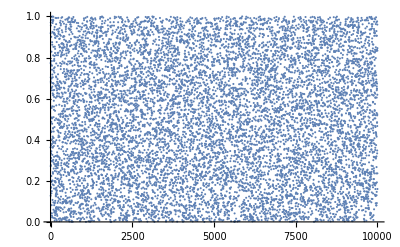

```mathematica
AbsoluteTiming[dwn=ParallelTable[RandomReal[],{i,10000}];]
ListPlot[dwn]
```

```mathematica
(* this works if github directory structure is the same as the local one, if not adjust accordling *)
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"Samplers","OwenScrambledSobol.nb"}]]
```

{2.17144,Null}

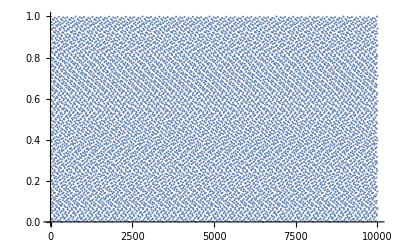

```mathematica
AbsoluteTiming[dos=ParallelTable[owenScrambledSobol1D[i],{i,10000}];]
ListPlot[dos]
```

See how the rectangle is more evenly filled with OwenScrambled(OS) than with WhiteNoise(WN) ? Yeah, OS is really slower compared to WN.

So, let’s see how it goes by sampling a function with our two different samplers.

{True value,2.}

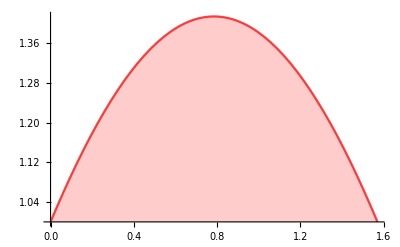

```mathematica
Clear[f,x,a,b, w, n, tValue, eValue];
f[x_]=Cos[x]+Sin[x];
a=0;
b=π/2;
w=b-a;
n=10000;
tValue = ∫_a^b f[x]ⅆx//N;
{"True value",tValue}

Plot[f[x],{x,a,b},Filling->Axis,PlotStyle->{Red, Opacity[0.75]},PlotRange->Full]
```

```mathematica
estsWN= ParallelTable[f[a+RandomReal[]*w],{i,n}]*w;
meanWN=Mean[estsWN]
```

1.99863

```mathematica
estsOS= ParallelTable[f[a+owenScrambledSobol1D[i]*w],{i,n}]*w;
meanOS=Mean[estsOS]
```

2.00001

To measure the impact of using a different sampler we of course will employ the error metrics we used above.
So let’s start by getting the standard deviation and its assoaciated Monte Carlo standard error and bias statistics.

```mathematica
Clear[sqr,MSE];
sqr=Sum[(estsWN[[i]]-tValue)^2,{i,n}];
{"STD WN",MSEwn=√(sqr/n) }(* aka standard deviation *)
{"MCSE WN",MCSEwn = √(Sum[((estsWN[[i]]-tValue)^2-MSEwn)^2,{i,n}]/(n*(n-1)))}

{"Bias WN",Sum[estsWN[[i]]-tValue,{i,m}] *(1/m)}
```

{STD WN,0.195335}

{MCSE WN,0.00162309}

{Bias WN,0.00314832}

```mathematica
Clear[sqr,MSE];
sqr=Sum[(estsOS[[i]]-tValue)^2,{i,n}];
{"STD OS",MSEos=√(sqr/n) }

{"MCSE OS",MCSE = √(Sum[((estsOS[[i]]-tValue)^2-MSEos)^2,{i,n}]/(n*(n-1)))}

{"Bias OS",Sum[estsOS[[i]]-tValue,{i,m}] *(1/m)}
```

{STD OS,0.195424}

{MCSE OS,0.00162208}

{Bias OS,0.000278994}

First let’s just note that with the STD and MCSE because of the squaring and then the square-rooting, - our errors look not so much different.
Bias instead, being an order of magnitude less for the OS sampler, gives us a somehow better statistic.

We can however also use a derivation (dependent t-test for paired samples) of the so called T-test that gives us a nice value that effectively seems characterezing a bit more our error.

```mathematica
DTtestwn=Abs[meanWN-tValue]/MSEwn
DTtestos=Abs[meanOS-tValue]/MSEos
```

0.00700643

0.0000435081

We can also use another derivation of the T-test called Welch’s t-test to compare directly our two estimates

t=((X^-)_1-(X^-)_2)/(√(s_1^2/N_1+s_2^2/N_2))

```mathematica
Twelch=(meanWN-meanOS)/(√(MSEwn^2/n+MSEos^2/n))
```

-0.498394

Eventually the T-test is given by

t=((X^-)_1-(X^-)_2)/(√((s_1^2+s_2^2)/2)*√(2/n))

```mathematica
(meanWN-meanOS)/(√((MSEwn^2+MSEos^2)/2)*√(2/n))
```

-0.498394

Result is the same of the Welch’s t-test because n is the same for both estimation there while it could be different as opposed to the T-test.


========================================================================================
Now this error estimates do tell us something when compared against different estimators of the same parameter (here mean).
What they don’t tell us is the variability of our result compared on successive runs of the same simulation.

```mathematica
meanWN
meanWN2= Mean[ParallelTable[f[a+RandomReal[]*w],{i,n}]*w]
meanWN3= Mean[ParallelTable[f[a+RandomReal[]*w],{i,n}]*w]
meanWN4= Mean[ParallelTable[f[a+RandomReal[]*w],{i,n}]*w]
meanWN5= Mean[ParallelTable[f[a+RandomReal[]*w],{i,n}]*w]
```

1.99863

2.00009

2.00038

2.00285

1.99925

```mathematica
SetPrecision[meanOS,18]
(*
meanOS2= Mean[ParallelTable[With[{i=i+n},f[a+owenScrambledSobol1D[i]*w]],{i,n}]*w]
meanOS3= Mean[ParallelTable[With[{i=i+n+n},f[a+owenScrambledSobol1D[i]*w]],{i,n}]*w]
meanOS4= Mean[ParallelTable[With[{i=i+n+n+n},f[a+owenScrambledSobol1D[i]*w]],{i,n}]*w]
meanOS5= Mean[ParallelTable[With[{i=i+n+n+n+n},f[a+owenScrambledSobol1D[i]*w]],{i,n}]*w]
*)

(*
u=5;
ddddd[x_]:=x;
ParallelTable[ With[{i=i},ddddd[i]],{i,u}]
ParallelTable[ With[{i=i+u},ddddd[i]],{i,u}]*)
```

2.00000850254700957

We already see what’s going on here.. for replicated simulation those with the OwenScrambledSobol sampler

========================================================================================

TODO: 
-> see examples for MC error estimates in -> Monte Carlo Simulations in Physics.pdf (desktop)
-> see Error Estimates in the MC Method.pdf (3.44)

-> https://bookdown.org/kevin_davisross/probbook/sec-cdf-method.html
-> https://bookdown.org/kevin_davisross/probbook/law-of-the-unconscious-statistician.html

-> https://www.scratchapixel.com/lessons/mathematics-physics-for-computer-graphics/monte-carlo-methods-mathematical-foundations/sampling-distribution
-> https://www.scratchapixel.com/lessons/mathematics-physics-for-computer-graphics/monte-carlo-methods-in-practice/monte-carlo-integration

# Basic Calculus with Mathematica

```mathematica
(*Integration Basics*)

(*Use 'ESC int ESC' to enter∫ .. and 'ESC dd ESC 'to enter ⅆ*)
(*Use CTRL_ to enter the lower limit,then CTRL% for the upper limit*)
(*or use the Basic Math Assistant palette*)
Clear[x];
∫_0^1 1/(x^3+1)ⅆx
%//N

Integrate[1/(x^3+1),{x,0,1}]
%//N
```

1/18 (2 √3 π+Log[64])

0.835649

1/18 (2 √3 π+Log[64])

0.835649

π

3.14159

π

3.1415926535897932385

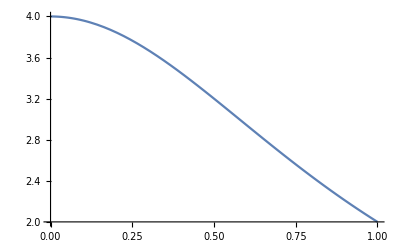

```mathematica
(*Calculate Pi(π) with integration*)
(*see LightTransport->theory->2014MonteCarloIntegration to integrate it with rnd samples.. aka 'crude qMC'*)
Clear[f];

f[x_]=4/(1+x^2);

Integrate[f[x],{x,0,1}]
%//N

∫_0^1 f[x]ⅆx
N[%,20] (*Pi with 20 digits precision*)

Plot[f[x],{x,0,1}]
```

```mathematica
(* Integration Strategies *)
(*https://reference.wolfram.com/language/tutorial/NIntegrateIntegrationStrategies.html*)

Timing[NIntegrate[E^-(x^4+y^4),{x,-2,2},{y,-2,2},Method->"MonteCarlo"]]
Timing[NIntegrate[E^-(x^4+y^4),{x,-2,2},{y,-2,2},Method->"QuasiMonteCarlo"]]
Timing[NIntegrate[E^-(x^4+y^4),{x,-2,2},{y,-2,2},Method->{"RiemannRule","Type"->"Right"},PrecisionGoal->2]]
Timing[NIntegrate[E^-(x^4+y^4),{x,-2,2},{y,-2,2},Method->{"NewtonCotesRule","Type"->"Closed"}]]
```

{0.019122,3.25507}

{0.053857,3.28632}

{0.045337,3.25423}

{0.110933,3.28626}

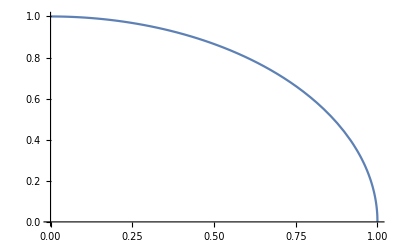

π/4

0.785398

```mathematica
Clear[f];
f[x_]:=Sqrt[1-x^2]
Plot[f[x], {x,0,1}]

Integrate[f[x],{x,0,1}]
%//N
```

see this: https://www.maplesoft.com/applications/view.aspx?sid=4009&view=html

-Graphics-

```mathematica
(* Hit-or-Miss Monte Carlo method to calculate π*)

(*The area ratio of a unit circle Ac over a unit square As is: Ac/As= πr^2 / 4r^2 = π/4 *)
(*We shoot (n) rnd pts over the square(-1,+1) and consider a hit for those pts (m) that satisfy: x^2+y^2≤1*)
(*Hence π = 4m/n ..ie. ratio of hit vs shot time 4*)

(*see 2013-Math Numerics and Programming (for mechanical engineers) ... *)
(*or MonteCarlo Integration in a Nutshell for better area estimation tecniques*)

Manipulate[
Module[{data,inside,insidepts},SeedRandom[n];
data=RandomReal[{-1,1},{m,2}];
insidepts=Cases[data,{x_,y_}/;x^2+y^2<1];
inside=Length[insidepts];
Text@Style[Column[{Graphics[{PointSize[0.004],RGBColor[0.86,0.5,0.74],Disk[{0,0},1],Black,Point[data]},ImageSize->If[format,500,350]],Row[{"inside: ",inside,"\toutside: ",m-inside,"\ttotal:  ",m}],Row[{"π ≈ 4 × ",inside,"/",m," = ",4. inside/m}]}],"Label"]
],
{{n,1,"random seed"},1,1000,1},{{m,64,"sample size"},64,8192,64,Appearance->"Labeled"},{{format,False,"large format"},{True,False}},AutorunSequencing->{1,2}]
```

{-0.006479,0.00486489}

-Graphics3D-

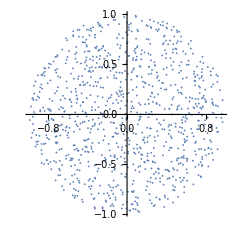

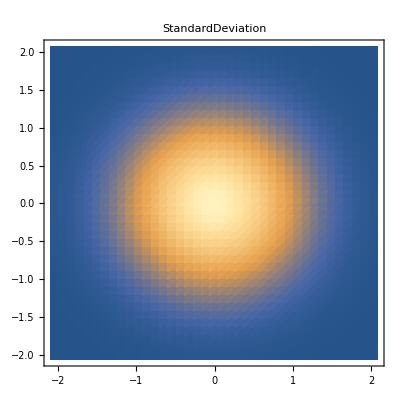
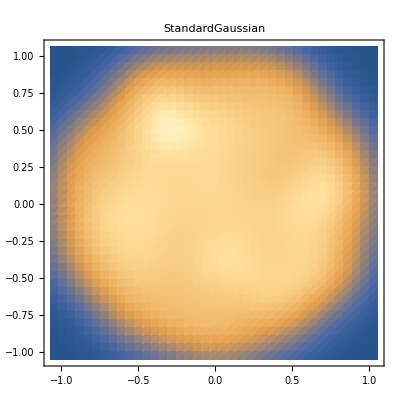

```mathematica
Clear[f,tf];
f[]:=Block[{u,t,r},
u=RandomReal[]+RandomReal[];
t=RandomReal[] 2 Pi;
r=If[u>1,2-u,u];
{r Cos[t],r Sin[t]}
]
tf=Table[f[],{1000}];

Mean[tf]
Histogram3D[tf,Automatic,"ProbabilityDensity",ChartElementFunction->"FadingCube"]
(*
SmoothHistogram[tf,50,"PDF",PlotRange->Automatic]
SmoothHistogram[tf,50,"CDF"]
*)
ListPlot[tf,AspectRatio->Automatic]
Table[SmoothDensityHistogram[tf,name,ImageSize->400,PlotLabel->name],{name,{"StandardDeviation","StandardGaussian"}}]
```

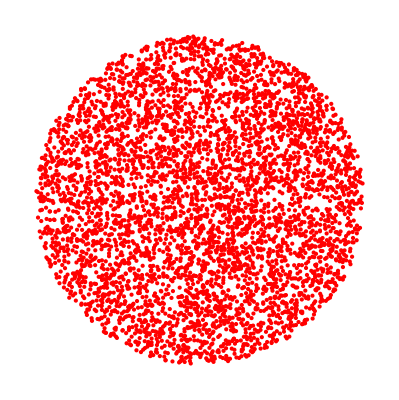

```mathematica
(*Generate a list of points in a unit disk.. new in M-11*)
pts=RandomPoint[Disk[],5000];
Graphics[{PointSize[Tiny],Red,Point[pts]}]
```

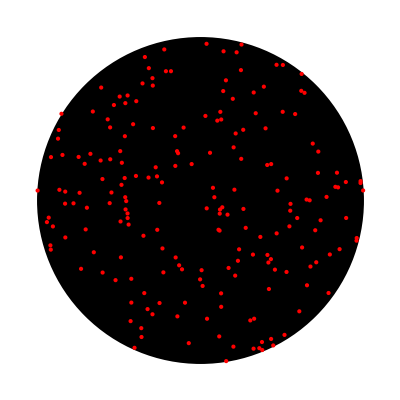
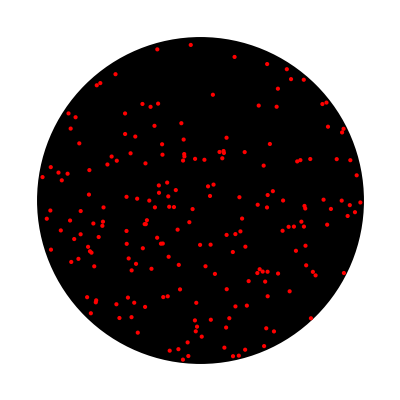
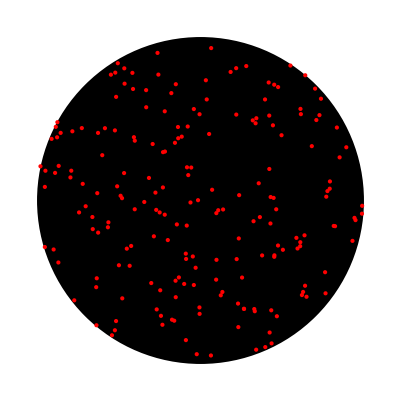

```mathematica
(*Generate multiple lists of points for a unit disk region*)
ℛ=Disk[];
pl=RandomPoint[ℛ,{3,200}];
Table[Graphics[{ℛ,Red,Point[pts]}],{pts,pl}]
```

{{0.05,15},{0.15,51},{0.25,64},{0.35,107},{0.45,113},{0.55,162},{0.65,163},{0.75,167},{0.85,182},{0.95,187},{1.05,165},{1.15,168},{1.25,151},{1.35,143},{1.45,121},{1.55,130},{1.65,109},{1.75,91},{1.85,91},{1.95,63},{2.05,48},{2.15,34},{2.25,29},{2.35,24},{2.45,14},{2.55,11},{2.65,6},{2.75,6},{2.85,9},{2.95,4},{3.05,4},{3.15,2},{3.25,0},{3.35,1},{3.45,5},{3.55,3},{3.65,2},{3.75,1},{3.85,2},{3.95,1},{4.05,0},{4.15,0}}

{ampl→274.765,x0→1.02404,sigma→0.614853}

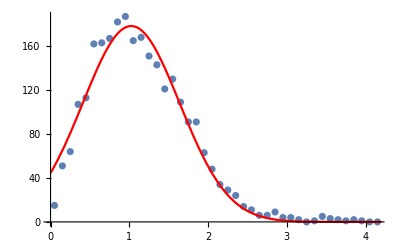

```mathematica
(*Gauss Fit to List of 2D Points*)
Clear[data,fit,sigma,x,ampl];
data={{0.05,15},{0.15,51},{0.25,64},{0.35,107},{0.45,113},{0.55,162},{0.65,163},{0.75,167},{0.85,182},{0.95,187},{1.05,165},{1.15,168},{1.25,151},{1.35,143},{1.45,121},{1.55,130},{1.65,109},{1.75,91},{1.85,91},{1.95,63},{2.05,48},{2.15,34},{2.25,29},{2.35,24},{2.45,14},{2.55,11},{2.65,6},{2.75,6},{2.85,9},{2.95,4},{3.05,4},{3.15,2},{3.25,0},{3.35,1},{3.45,5},{3.55,3},{3.65,2},{3.75,1},{3.85,2},{3.95,1},{4.05,0},{4.15,0}}
model[x_]=ampl Evaluate[PDF[NormalDistribution[x0,sigma],x]];
fit=FindFit[data,model[x],{ampl,x0,sigma},x]

(*{ampl->274.765,x0->1.02404,sigma->0.614853}*)

Show[ListPlot[data],Plot[model[x]/.fit,{x,0,4.2},PlotStyle->Red]]
```

ae^(-1/2 c^2 (-b+x)^2)

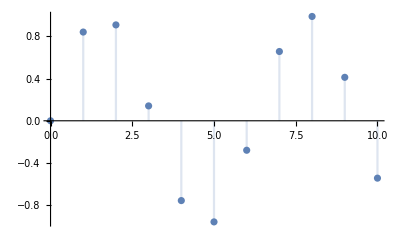

```mathematica
(*DiracComb to sample a function*)
Clear[x,a,b,c,e,f];
f[x]=ae^-((x-b)^2/2c^2)(*gaussian fnc*)
DiscretePlot[Sum[DiscreteDelta[t-n] Sin[t],{n,Infinity}],{t,0,10}]
```

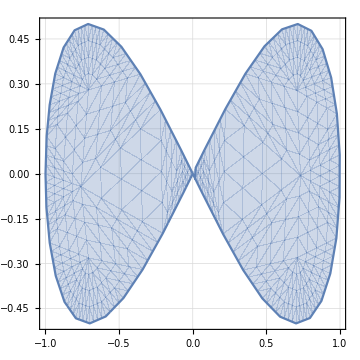

0.812698

```mathematica
(*Integrate a fnc over a parametric domain ... new in M-11*)
Clear[f,x,y, region];
region=ParametricRegion[{{s,s t},s^2+t^2≤1},{s,t}];
RegionPlot[region,ImageSize->Medium,PlotTheme->"Detailed",PlotLegends->None]

f[{x_,y_}]:=x^3-2 x^2 y+4 x^6-y^5;
val=NIntegrate[f[{x,y}],{x,y}∈region]

(*visualize the convergence of the Monte Carlo statistic as the sample size increases*)
(* uncomment it as it takes time to get resolved *)
(*
ListLogLogPlot[Transpose[{2^Range[20],ParallelTable[RegionMeasure[region] Mean[f/@RandomPoint[region,2^n]],{n,1,20}]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->Medium,Joined->True,Filling->val]
*)
```

```mathematica
(* Use Monte Carlo sampling to calculate the area of the white area in the figure below *)
pannter=ImageData[Image[ColorConvert[-Graphics-,GrayLevel],"Bit"]];
n=100000;Total[Table[If[pannter[[RandomInteger[{1,Dimensions[pannter][[1]]}],RandomInteger[{1,Dimensions[pannter][[2]]}]]]==1,1,0],{n}]]/n //N

(* Compare with a direct count of bright points,1s,with dark points (0s): *)
Count[Flatten[pannter],0];
N[Count[Flatten[pannter],1]/Length[Flatten[pannter]]]
```

0.36432

0.366691

# Stochastic Processes

Till now what we’ve seen it’s more about general statistical methods powered by probability theory. The average life expectancy of a population, what’s the probability of having a female baby after two males ;) etc. If you’re still interested in that, better go elsewhere to study them in detail.
From now on we’ll focus on Computer Science and Computer Graphics probabilistic/stochastics approaches.

Let’s start trying to understand what is a determinist approach vs a stochastic one.

A deterministic model generally does not include elements of randomness. Every time one runs a model with the same initial conditions he will get the same results. Most simple mathematical models of everyday situations are deterministic, for example, the height (h) in metres of an apple dropped from a hot air balloon at 300m could be modelled by h = - 5t2 + 300, where t is the time in seconds since the apple was dropped.

However let’s say that we can’t exactly measure the height from where the apple is dropped and neither exactly the time it take to fall on the ground, or better let’s say the those measure are slighty different every time we redo the simulation. How to deal with that ? With a probabilist approach. A probabilistic model includes elements of randomness. Every time one runs the model, he’s likely to get different results, even with the same initial conditions. A probabilistic model is one which incorporates some aspect of random variation.

A deterministic model is a model where:
1 - the material properties are well known, i.e. deterministic. none of them is random
2 - The applied load are also deterministic

A Stochastic model has on the other hand:
1 - random properties; or normal distribution (of a given mean or standard deviation)
2 - the applied load is random variable, e.g. wind Load, earthquake (vibration of random amplitude and displacement)

A deterministic model is one that uses numbers as inputs, and produces numbers as outputs. 

A stochastic model includes a random component that uses a distribution as one of the inputs, and results in a distribution for the output. These distributions may reflect the uncertainty in what the input should be (e.g. a deterministic input plus noise), or may reflect a random process (i.e. a stochastic input).

For example we can use a deterministic approach if all we want is to shoot a couple of rays and analyse their hit. 
However it’s better we use a stochastic approach if you wanna run a simulation with milions of rays and evaluate their intersections. 

The notion of a stochastic processes is very important both in mathematical theory and its applications in science, engineering, economics, etc. 
It is used to model a large number of various phenomena where the quantity of interest varies discretely or continuously through time in a non-predictable fashion. 
Every stochastic process can be viewed as a function of two variables - t and ω. For each fixed t, ω → Xt(ω) is a random variable, as postulated in the definition. However, if we change our point of view and keep ω fixed, we see that the stochastic process is a function mapping ω to the real-valued function t → Xt(ω). These functions are called the trajectories of the stochastic process X.

Now, let’s start to see a bit more in detail a stochastic process.

A stochastic process {Xn}n ∈ ℕ_0 is called a simple random walk if :
- X0 = 0,
- the increment Xn+1 − Xn is independent of (X0, X1, . . . , Xn) for each n ∈ ℕ_0, and
- the increment Xn+1 − Xn has the coin-toss distribution

On the other side, a random walk is called ‘simple’ when the size of each step is fixed (equal to 1) and it is only the direction that is random.

Below are all applications of a simple random walk using different Mathematica approaches that have all a common thing ... 
a random variate to generate the next direction  :

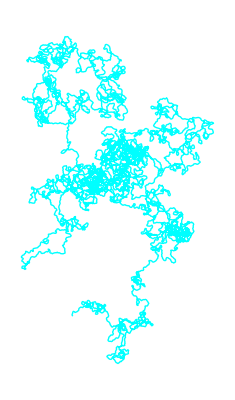

```mathematica
Block[{size=0.5},
l=Line[
Accumulate[
Function[x,size*{Re[x],Im[x]},Listable]
[Exp[I 
Accumulate[
RandomVariate[
NormalDistribution[0,Pi/4],
10^4]]]]]];
Graphics[{Cyan,l}]
]
```

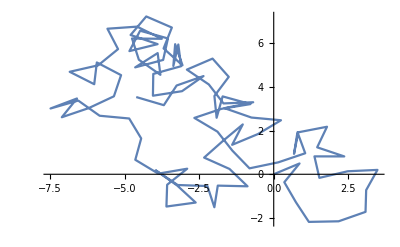

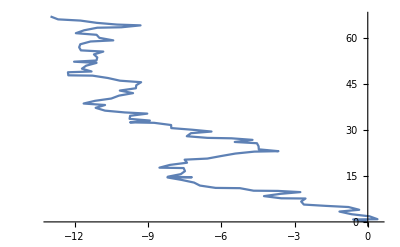

```mathematica
(* random walk for ω ∈ {0,2π}, ie. at any new segment we can turn up to 360°*)
randomWalk2D[t_]:=Accumulate[Prepend[
RandomPoint[DiscretizeRegion[Circle[]],t],
{0,0}]]//ListLinePlot
randomWalk2D[100]

(* forward biased random walk for ω ∈ {0,π}, ie. at any new segment we can turn up to 180°, aka never look back *)
hemicircle = Circle[{0,0},1,{0,Pi}];
randomWalk2Dforward[t_]:=Accumulate[Prepend[
RandomPoint[DiscretizeRegion[hemicircle],t],
{0,0}]]//ListLinePlot
randomWalk2Dforward[100]

(* use 'sphere' instead of 'circle' and {0,0,0} instead of {0,0} for 3D walks *)
```

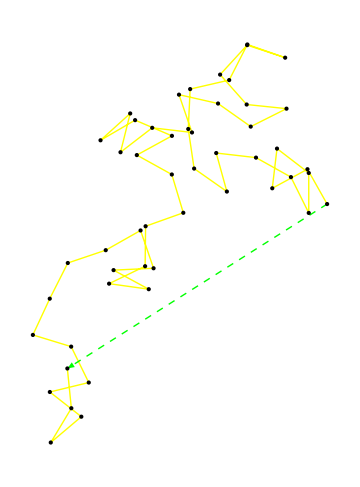

7.68086

```mathematica
(* 2D simple random walk *)

step[position_]:=With[{t=2Pi RandomReal[]},position+{Cos[t],Sin[t]}];
walk[n_,origin_: {0,0}]:=NestList[step,origin,n];
distance[aWalk_]:=EuclideanDistance@@aWalk[[{1,-1}]]; (* calc dist between first and last pt in the walk list *)
draw[aWalk_]:=Graphics[{Yellow,Line[aWalk],Dashed,Green,Arrowheads[Large],Arrow[aWalk[[{1,-1}]]],Black,PointSize[Medium],Point[aWalk]},ImageSize->Medium];

step[{10,0}];
w=walk[50];
draw[w]
distance[w]
```

```mathematica
(* 3D simple random walk *)

Clear[step,walk,distance,draw]; 

(* comment this out to have everytime a different random walk as above *)
SeedRandom[12345]; 

(* change t to Pi for forward only directions for example *)
step[position_: {0,0,0}]:=With[{t=2Pi RandomReal[],p=Pi RandomReal[]},position+{Cos[t]Sin[p],Sin[t]Sin[p],Cos[p]}];

walk[n_,origin_: {0,0,0}]:=NestList[step,origin,n];
distance[aWalk_]:=EuclideanDistance@@aWalk[[{1,-1}]]; (* calc dist between first and last pt in the walk list *)
draw[aWalk_]:=Graphics3D[{Cyan,Line[aWalk],Dashed,Green,Arrowheads[Large],Arrow[aWalk[[{1,-1}]]],Red,PointSize[Medium],Point[aWalk]},ImageSize->Large,ViewProjection->"Orthographic",ViewPoint->{Pi,Pi/2,2}];

distance[w]
draw[walk[100]]
```

7.68086

-Graphics3D-

Simulate and plot multiple paths of the following stochastic difference equation, 
for any initial condition π0∈(0,1): πt+1=γπt with probability 1/3πt and πt+1=(1−γ)πt with probability 2/3πt, where γ∈(0,1) is a parameter.

0.876608

0.521964

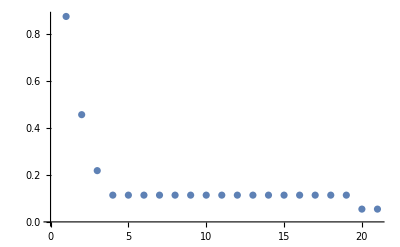

```mathematica
Clear[pi0,gamma];
SeedRandom[1234];
pi0=RandomReal[]
gamma=RandomReal[]
nextpi[pi_]:=RandomChoice[{1/3*pi,2/3*pi,1-pi}->{gamma*pi,(1-gamma)*pi,pi}]
trajectory=NestList[nextpi,pi0,20];
ListPlot[trajectory]
```